## ToyScan1

This Mathematica notebook plots the Markov chains obtained by running ToyScan1.  As defined in main.cpp, this scan uses 10 chains and 10k steps to seek out the point (1, 1, 1) with a Gaussian likelihood profile, with uncertainties (0.1, 0.5, 1.0).

### Import and parse the chains

```mathematica
SetDirectory[NotebookDirectory[]];

Chains={};
Module[{i,FileData},
For[i=1,i≤10,i++,
FileData=Import["chains/ToyScan1_chain"<>ToString[i]<>".dat"];
AppendTo[Chains,Split[FileData,#≠{}&]]
]
]
```

```mathematica
Chains[[1,1;;10]]//MatrixForm
```

({0.382377,7.95707,-9.91522} | {12.9586,2.57236,-1.48225} | {6.38286×10^-77} | {}
{0.382377,7.95707,-9.91522} | {12.9586,2.57236,-1.48225} | {6.38286×10^-77} | {}
{0.632815,8.86367,-1.28692} | {8.19769,1.85352,-1.52414} | {1.68026×10^-58} | {}
{0.632815,8.86367,-1.28692} | {8.19769,1.85352,-1.52414} | {1.68026×10^-58} | {}
{0.632815,8.86367,-1.28692} | {8.19769,1.85352,-1.52414} | {1.68026×10^-58} | {}
{0.632815,8.86367,-1.28692} | {8.19769,1.85352,-1.52414} | {1.68026×10^-58} | {}
{0.632815,8.86367,-1.28692} | {8.19769,1.85352,-1.52414} | {1.68026×10^-58} | {}
{1.41015,9.20467,1.92356} | {8.26667,1.45884,1.52085} | {4.91249×10^-63} | {}
{1.41015,9.20467,1.92356} | {8.26667,1.45884,1.52085} | {4.91249×10^-63} | {}
{1.41015,9.20467,1.92356} | {8.26667,1.45884,1.52085} | {4.91249×10^-63} | {})

### Setting up accessor functions

```mathematica
ChainLength[iChain_]:=Length[Chains[[iChain]]];

Parameters[iChain_,iPoint_]:=Chains[[iChain,iPoint,1]];
r[iChain_,iPoint_]:=Chains[[iChain,iPoint,2,1]];
θ[iChain_,iPoint_]:=Chains[[iChain,iPoint,2,2]];
ϕ[iChain_,iPoint_]:=Chains[[iChain,iPoint,2,3]];
NegativeLogLikelihood[iChain_,iPoint_]:=-Log[10,Chains[[iChain,iPoint,3,1]]];
```

### Plotting the chains

Here I plot the full chains, from beginning to end, without burning the initial fraction.  The different colors correspond to different chains.

```mathematica
ListPointPlot3D[Parameters[All,All],PlotRange->{{-5,5},{-5,5},{-5,5}},ImageSize->Large]
```

-Graphics3D-

### Plotting distance from the target point

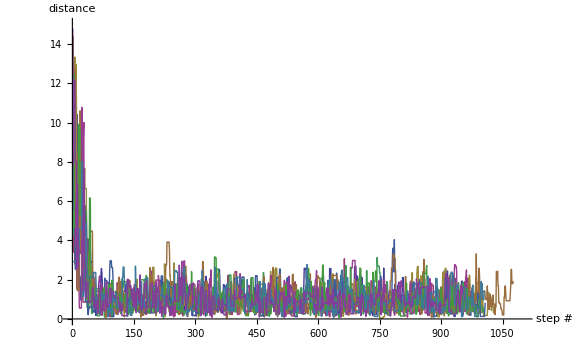

```mathematica
ListPlot[r[All,All],Joined->True,PlotRange->{{0,1100},{0,15}},AxesLabel->{"step #","distance"},ImageSize->Large]
```

### Plotting likelihood

This plots the negative log-likelihood of the points in the chains.  It shows how many orders of magnitude below likelihood == 1.0 (which indicates perfect agreement with the target point) the likelihood is at.  As the chains’ likelihood increases, the negative log-likelihood approaches zero.

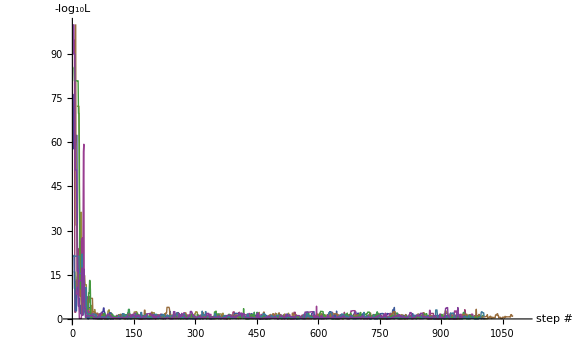

```mathematica
ListPlot[NegativeLogLikelihood[All,All],Joined->True,PlotRange->{{0,1100},{0,100}},AxesLabel->{"step #","-log_10L"},ImageSize->Large]
```